```mathematica
RSolve[{a[n+2]==a[n+1]+a[n]+n,a[0]==1,a[1]==2},a[n],n]
```

{{a[n]→1/(5 (1+√5)^2)(2 (-1-√5))^-n (-35 (-4)^n Fibonacci[n]-15 (-4)^n √5 Fibonacci[n]+45 2^(1+n) (-1-√5)^n Fibonacci[n]+15 2^(1+n) √5 (-1-√5)^n Fibonacci[n]-10 (-1-√5)^(2 n) Fibonacci[n]-5 (-1)^n 2^(2+2 n) n Fibonacci[n]-5 (-1)^n 2^(1+2 n) √5 n Fibonacci[n]+5 (-1-√5)^(2 n) n Fibonacci[n]+5 √5 (-1-√5)^(2 n) n Fibonacci[n]-15 (-4)^n LucasL[n]-7 (-4)^n √5 LucasL[n]+15 2^(1+n) (-1-√5)^n LucasL[n]+5 2^(1+n) √5 (-1-√5)^n LucasL[n]+2 √5 (-1-√5)^(2 n) LucasL[n]-5 (-1)^n 2^(1+2 n) n LucasL[n]-(-1)^n 2^(2+2 n) √5 n LucasL[n]-5 (-1-√5)^(2 n) n LucasL[n]-√5 (-1-√5)^(2 n) n LucasL[n])}}

```mathematica
RSolve[{a[n+2]==a[n+1]+a[n],a[0]==1,a[1]==2},a[n],n]
```

{{a[n]→1/2 (3 Fibonacci[n]+LucasL[n])}}

```mathematica
f1[n_]:=1/(5 (1+√5)^2)(2 (-1-√5))^-n (-35 (-4)^n Fibonacci[n]-15 (-4)^n √5 Fibonacci[n]+45 2^(1+n) (-1-√5)^n Fibonacci[n]+15 2^(1+n) √5 (-1-√5)^n Fibonacci[n]-10 (-1-√5)^(2 n) Fibonacci[n]-5 (-1)^n 2^(2+2 n) n Fibonacci[n]-5 (-1)^n 2^(1+2 n) √5 n Fibonacci[n]+5 (-1-√5)^(2 n) n Fibonacci[n]+5 √5 (-1-√5)^(2 n) n Fibonacci[n]-15 (-4)^n LucasL[n]-7 (-4)^n √5 LucasL[n]+15 2^(1+n) (-1-√5)^n LucasL[n]+5 2^(1+n) √5 (-1-√5)^n LucasL[n]+2 √5 (-1-√5)^(2 n) LucasL[n]-5 (-1)^n 2^(1+2 n) n LucasL[n]-(-1)^n 2^(2+2 n) √5 n LucasL[n]-5 (-1-√5)^(2 n) n LucasL[n]-√5 (-1-√5)^(2 n) n LucasL[n])
```

```mathematica
f2[n_]:=1/2 (3 Fibonacci[n]+LucasL[n])
```

```mathematica
f[1.2]
```

0.0189595-0.0764894 ⅈ

```mathematica
f[4.]
```

3.+1.41786×10^-15 ⅈ

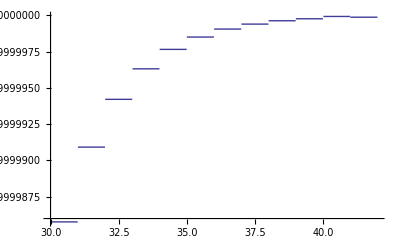

```mathematica
Plot[Re[f1[Floor[x]]]/Re[f2[Floor[x]]],{x,30,42}]
```

```mathematica
f1[34.]/f2[34]
```

2.-4.84729×10^-21 ⅈ